高对称四方反铁磁体：自旋对称性与 SOC

下面考虑磁空间群为 124.360，P_c4/mcc 的四方反铁磁模型。群中 32 个操作生成 z=0 和 z=1/2 两个磁矩相反的位置。我们比较有、无自旋轨道耦合（SOC）时的 Hamiltonian 和能带。由于 onsite SOC 会混合不同的 p 轨道和自旋，这里保留 px、py、pz 的全部自旋分量。

```mathematica
Needs["MagneticTB`"]
```

含 SOC 的高对称 MSG 124.360

有 SOC 时，自旋旋转与空间操作相联系。把完整磁空间群传给 init，再求 onsite 项和两层之间的最近邻跃迁：

```mathematica
init[
  lattice -> DiagonalMatrix[{a, a, c}],
  lattpar -> {a -> 1, c -> 3/2},
  wyckoffposition -> {{{0, 0, 0}, {0, 0, 1}}},
  symminformation -> msgop[typeIV[{124, 360}]],
  basisFunctions -> {{
    "pxup", "pxdn", "pyup", "pydn", "pzup", "pzdn"
  }},
  InitialBondShells -> 2
];
socHamiltonian = symham[1] + symham[2];
socRepresentation = CurrentModelSession[][
  "FullRepresentation", "RepresentationMatrices"
];
```

```mathematica
showCrystalStructure[]
```

-Graphics3D-

两层的磁矩方向相反。下面的 6 × 6 矩阵是 z=0 层的 onsite 子块，行列顺序为 {pxup,pxdn,pyup,pydn,pzup,pzdn}：

```mathematica
MatrixForm[symham[1][[1 ;; 6, 1 ;; 6]]]
```

(-e8 | 0 | ⅈ e4 | 0 | 0 | -e1
0 | -e7 | 0 | ⅈ e3 | e2 | 0
-ⅈ e4 | 0 | -e8 | 0 | 0 | ⅈ e1
0 | -ⅈ e3 | 0 | -e7 | ⅈ e2 | 0
0 | e2 | 0 | -ⅈ e2 | -e6 | 0
-e1 | 0 | -ⅈ e1 | 0 | 0 | -e5)

无 SOC：加入连续 C-infinity 自旋对称性

无 SOC 时，还可以绕磁化轴独立旋转自旋。把有限操作写成自旋空间群，再加上这个连续的 C_infinity 对称性。下面使用前一个模型得到的有限群表示矩阵，与连续旋转一起传给 initfromrep。

```mathematica
initfromrep[
  lattice -> DiagonalMatrix[{a, a, c}],
  lattpar -> {a -> 1, c -> 3/2},
  wyckoffposition -> {{{0, 0, 0}, {0, 0, 1}}},
  symminformation -> Append[
    Association @ MapIndexed[
      "g" <> ToString[#2[[1]]] -> <|
        "space" -> #1[[{2, 3}]],
        "spin" -> {
          Det[#1[[2]]] #1[[2]], Boole[#1[[4]] == "T"]
        }
      |> &,
      msgop[typeIV[{124, 360}]]
    ],
    "C_infty" -> <|
      "space" -> {IdentityMatrix[3], {0, 0, 0}},
      "spin" -> {{
        {Cos[theta], -Sin[theta], 0},
        {Sin[theta], Cos[theta], 0},
        {0, 0, 1}
      }, 0},
      "continuous" -> theta
    |>
  ],
  repinformation -> <|
    "Discrete" -> {MapThread[
      Function[{matrix, operation},
        With[{site = First@FirstPosition[
            First@CurrentModelSession[][
              "ModelSpecification", "SiteOrbits"
            ],
            Mod[operation[[3]], 1]
          ]},
          matrix[[6 (site - 1) + Range[6], Range[6]]]
        ]
      ],
      {socRepresentation, msgop[typeIV[{124, 360}]]}
    ]},
    "Continuous" -> <|
      "SiteMatrices" -> {ConstantArray[
        KroneckerProduct[
          IdentityMatrix[3],
          DiagonalMatrix[{Exp[-I theta/2], Exp[I theta/2]}]
        ],
        2
      ]}
    |>
  |>,
  orbitalLabels -> {{
    "pxup", "pxdn", "pyup", "pydn", "pzup", "pzdn"
  }},
  InitialBondShells -> 2
];
noSOCHamiltonian = symham[1] + symham[2];
```

```mathematica
MatrixForm[symham[1][[1 ;; 6, 1 ;; 6]]]
```

(e1 | 0 | ⅈ e5 | 0 | 0 | 0
0 | e2 | 0 | ⅈ e6 | 0 | 0
-ⅈ e5 | 0 | e1 | 0 | 0 | 0
0 | -ⅈ e6 | 0 | e2 | 0 | 0
0 | 0 | 0 | 0 | e3 | 0
0 | 0 | 0 | 0 | 0 | e4)

对比两个 onsite 矩阵，可以看到加入 C_infinity 后，px/py 与 pz 之间混合自旋的项变为零。保留 onsite 和最近邻跃迁时，有 SOC 的模型含 13 个实参数，无 SOC 时为 9 个：

```mathematica
{
  Length[Variables[socHamiltonian]],
  Length[Variables[noSOCHamiltonian]]
}
```

{13,9}

沿 G-Z 的能带劈裂

最近邻沿 c 方向分布，下面沿 G-Z 画能带。为了看清区别，两种模型都只取一个非零跃迁参数，有 SOC 时再打开前面矩阵中的两个 onsite 自旋轨道混合项。

有 SOC 时的能带为：

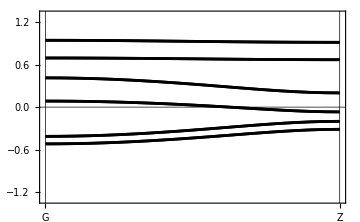

```mathematica
bandplot[
  {{{{0, 0, 0}, {0, 0, 1/2}}, {"G", "Z"}}},
  20,
  socHamiltonian /. Thread[
    {e1, e2, e3, e4, e5, e6, e7, e8, t1, t2, t3, t4, t5} ->
    {0.25, 0.25, 0, 0, -0.8, -0.4, -0.2, 0.2, -0.18, 0, 0, 0, 0}
  ],
  {},
  plotRange -> {-1.3, 1.3}, FontSize -> 18, ImageSize -> 360
]
```

无 SOC，并加入 C_infinity 对称性后，能带为：

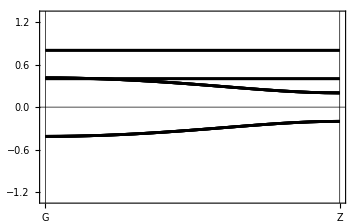

```mathematica
bandplot[
  {{{{0, 0, 0}, {0, 0, 1/2}}, {"G", "Z"}}},
  20,
  noSOCHamiltonian /. Thread[
    {e1, e2, e3, e4, e5, e6, t1, t2, t3} ->
    {-0.2, 0.2, 0.4, 0.8, 0, 0, -0.18, 0, 0}
  ],
  {},
  plotRange -> {-1.3, 1.3}, FontSize -> 18, ImageSize -> 360
]
```

在这组参数下，有 SOC 时 G 点有六组二重简并能级；无 SOC 时，G 点的简并度为 {4,2,4,2}。这里的四重简并出现在高对称点，并不是整条路径都四重简并。

连续接口的适用范围

initfromrep 这里接受一个没有空间作用的纯内部 C_infinity 连续旋转。有限群必须完整，表示矩阵要与群元顺序一一对应。连续旋转只约束局域态，不会生成更多原子、补全有限群或增加近邻跃迁。

typeIV ▪ init ▪ initfromrep ▪ symham ▪ bandplot ▪ showCrystalStructure ▪ MagneticTB

历史